# In this file, we use Z-wire only and turn on anharmonicity for the DKC trap

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Trap center (m):

{x→-2.35599×10^-11,y→8.05043×10^-14,z→0.000561498}

Trap frequencies (Hz):

{100.18,99.1978,1.06868}

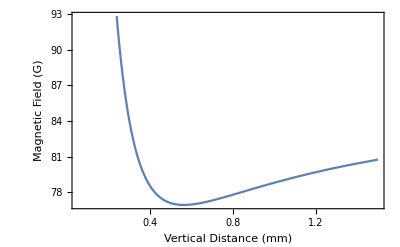
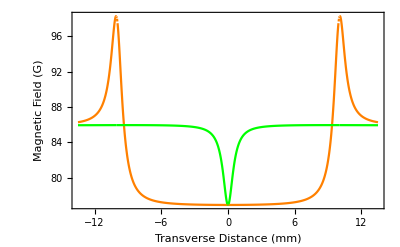
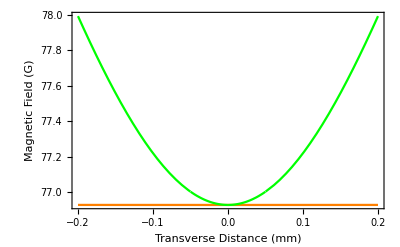

```mathematica
<<PhysicalConstants`
t=.;
Kilogram=Meter=Joule =Second=Kelvin=1;
T = 18*10^-9; (* Temperature in K *)
fc = 0.5; (* fraction of condensed atoms *)

m =87*ProtonMass;
a=104.5*BohrRadius; (* scattering length *)
hbar=PlanckConstantReduced;
kb = BoltzmannConstant;

μm=10^-6;
k=10^-7;
mA=mm=10^-3;
μ0=4π 10^-7;

(* Function FatXwire calculates the magnetic field at position (x0,y0,z0) of a rectangular conductor with finite width 2*hw.  We assume: (1) Current flows in the x direction from x1 -> x2; (2) The conductor is centered at y=yc and has width 2*hw; (3) The conductor lies entirely in the x-y plane (i.e. z=0). *)
FatXwire[x0_,y0_,z0_,hw_,yc_,x1_,x2_]:=Module[{dx1,dx2,dyPlus,dyMinus},
dx1=-x0+x1;
dx2=-x0+x2;
dyPlus=hw-y0+yc;
dyMinus=hw+y0-yc;
Return[10^-3/(2hw){0,ArcTan[(dx1 dyMinus)/(z0 √(dx1^2+dyMinus^2+z0^2))]-ArcTan[(dx2 dyMinus)/(z0 √(dx2^2+dyMinus^2+z0^2))]+ArcTan[(dx1 dyPlus)/(z0 √(dx1^2+dyPlus^2+z0^2))]-ArcTan[(dx2 dyPlus)/(z0 √(dx2^2+dyPlus^2+z0^2))],Log[(dx1+√(dx1^2+dyMinus^2+z0^2))/(dx2+√(dx2^2+dyMinus^2+z0^2))(dx2+√(dx2^2+dyPlus^2+z0^2))/(dx1+√(dx1^2+dyPlus^2+z0^2))]}];
];

(* Function FatYwire calculates the B-field at position (x0,y0,z0) for a conductor of width 2*hw at position x=xc running a finite length in y from y1->y2. We assume the conductor lies in the plane z=0. *)
FatYwire[x0_,y0_,z0_,hw_,xc_,y1_,y2_]:=Module[{dxPlus,dxMinus,dy1,dy2},
dxPlus=hw+x0-xc;
dxMinus=hw-x0+xc;
dy1=y0-y1;
dy2=-y0+y2;
Return[10^-3/(2 hw){(ArcTan[(dxPlus dy1)/(z0 √(dxPlus^2+dy1^2+z0^2))]+ArcTan[(dxMinus dy1)/(z0 √(dxMinus^2+dy1^2+z0^2))]+ArcTan[(dxPlus dy2)/(z0 √(dxPlus^2+dy2^2+z0^2))]+ArcTan[(dxMinus dy2)/(z0 √(dxMinus^2+dy2^2+z0^2))]),0,-Log[(-dy1+√(dxPlus^2+dy1^2+z0^2))/(-dy1+√(dxMinus^2+dy1^2+z0^2))(dy2+√(dxMinus^2+dy2^2+z0^2))/(dy2+√(dxPlus^2+dy2^2+z0^2))]}];
];
(* Pick a coordinate system: "x" is the direction of the main chip wire, and "y" is the direction current flows along the dimple. *)
ChipTrapField[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=Module[{VecField},
VecField=Ix*FatXwire[x,y,z,50μm,0,-10mm,+10mm] (* main section of Z wire *)
+Ix*FatYwire[x,y,z,50μm,-10mm,-10mm,0mm] (* first leg of Z wire *)
+Ix*FatYwire[x,y,z,50μm,10mm,0mm,10mm] (* second leg of Z wire *)
+Iy*FatYwire[x,y,z,50μm,0,-10mm,10mm]+{Bx,By,0}; (* dimple wire *)
Return[Sqrt[VecField.VecField]]
]

z0[Ix_,Iy_,Bx_,By_]:=NMinimize[{ChipTrapField[x,y,z,Ix,Iy,Bx,By],-0.5mm<x<0.5mm,-0.5mm<y<0.5mm,2000μm>z>3μm},{x,y,z}][[2]]

μB =9.27*10^-24; (* J/T *) (* Put correct value for Rb! *)

mRb = 1.443*10^-25; (* kg *)
Dxx[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],{x,2}];
Dxy[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],x,y];
Dxz[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],x,z];
Dyy[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],{y,2}];
Dyz[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],y,z];
Dzz[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=D[10^-4 ChipTrapField[x,y,z,Ix,Iy,Bx,By],{z,2}];
DMatrix[x_,y_,z_,Ix_,Iy_,Bx_,By_]:=({{Dxx[x,y,z,Ix,Iy,Bx,By], Dxy[x,y,z,Ix,Iy,Bx,By], Dxz[x,y,z,Ix,Iy,Bx,By]}, {Dxy[x,y,z,Ix,Iy,Bx,By], Dyy[x,y,z,Ix,Iy,Bx,By], Dyz[x,y,z,Ix,Iy,Bx,By]}, {Dxz[x,y,z,Ix,Iy,Bx,By], Dyz[x,y,z,Ix,Iy,Bx,By], Dzz[x,y,z,Ix,Iy,Bx,By]}});

(* The funciton ChipTrapFrequencies calculates the position z0 where the trap is centered. It does this using the values for the chip currents and bias fields. It assumes the trap is centered at x=0 and y=0 *)
ChipTrapFrequencies[Ix_,Iy_,Bx_,By_]:= Module[{x,y,z,DMatrixDiag,xmin,ymin,zmin},
{xmin,ymin,zmin}=z0[Ix,Iy,Bx,By];
xmin=xmin[[2]];
ymin=ymin[[2]];
zmin=zmin[[2]];
DMatrixDiag=Eigensystem[DMatrix[x,y,z,Ix,Iy,Bx,By]/.{x->xmin,y->ymin,z->zmin}];
Return[
 Sqrt[μB Abs[DMatrixDiag[[1]]]/mRb]/(2π) (* in Hz *)
]
]

A=34;  (* treat A as a scaling parameter *)
CLg1=-.32*A; (* main Z-wire current; flows in x direction in these coordinates, z direction in cart coordinates *)(* -3.250 *)
CLd1=0.1*A*0;(* dimple wire current; flows in y direction in these coordinates, x direction in cart coordinates *)
Bx1=-0.1*22.6*1*A;  (* Bias field in x direction (these coordinates) or z direction (cart coordinates *)
By1=-0.05*22.6*1*A; (* Bias field in y direction (these coordinates) or x direction (cart coordinates *)

Print["Trap center (m):"]
{x1,y1,z1}=z0[CLg1,CLd1,Bx1,By1]
x1=x1[[2]];
y1=y1[[2]];
z1=z1[[2]];

Bmin1=ChipTrapField[x1,y1,z1,CLg1,CLd1,Bx1,By1];
Depth1=ChipTrapField[x1,y1,1,CLg1,CLd1,Bx1,By1]-Bmin1;
Print["Trap frequencies (Hz):"]
freqs1=ChipTrapFrequencies[CLg1,CLd1,Bx1,By1]
(*

Print["Level of cubic anharmonicity for the vertical field strength (should be <<1):"]
Lint=100*√((kb*T)/m)/(2π*freqs1[[1]]); (* here 100 is Sqrt[Ti/Tf] *)
Lint*SeriesCoefficient[ChipTrapField[x1,y1,z1+x,CLg1,CLd1,Bx1,By1],{x,0,3}]/SeriesCoefficient[ChipTrapField[x1,y1,z1+x,CLg1,CLd1,Bx1,By1],{x,0,2}]
Print["Level of cubic anharmonicity for the horizontal field strength (should be <<1):"]
Lint=100*√((kb*T)/m)/(2π*freqs1[[2]]); (* here 100 is Sqrt[Ti/Tf] *)
Lint*SeriesCoefficient[ChipTrapField[x1,y1+x,z1,CLg1,CLd1,Bx1,By1],{x,0,3}]/SeriesCoefficient[ChipTrapField[x1,y1+x,z1,CLg1,CLd1,Bx1,By1],{x,0,2}]


*)
Plot1=Plot[ChipTrapField[x1,y1,z mm,CLg1,CLd1,Bx1,By1],{z,0.05,1.5},
Frame->True,Axes->False,
FrameLabel->{"Vertical Distance (mm)","Magnetic Field (G)"},
LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None],
Background->White,
ImageSize->400
];
Plot2=Plot[{ChipTrapField[x mm,y1,z1,CLg1,CLd1,Bx1,By1],ChipTrapField[x1,x mm,z1,CLg1,CLd1,Bx1,By1]},{x,-13.5,13.5},PlotStyle->{Orange,Green},
Frame->True,Axes->False,
FrameLabel->{"Transverse Distance (mm)","Magnetic Field (G)"},
LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None],
Background->White,
ImageSize->400
];
Plot3=Plot[{ChipTrapField[x mm,y1,z1,CLg1,CLd1,Bx1,By1],ChipTrapField[x1,x mm,z1,CLg1,CLd1,Bx1,By1]},{x,-.2,.2},PlotStyle->{Orange,Green},
Frame->True,Axes->False,
FrameLabel->{"Transverse Distance (mm)","Magnetic Field (G)"},
LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None],
Background->White,
ImageSize->400
];
{Plot1, Plot2, Plot3}
(*Ldist=10;
dplot3d=Plot3D[ChipTrapField[x mm,y mm,z1,CLg1,CLd1,Bx1,By1],{x,-Ldist,Ldist},{y,-Ldist/10,Ldist/10},AxesLabel->{"x (mm)", "y (mm)","B(G)     "},LabelStyle->Directive[FontFamily->"Arial",Bold,FontSize->14,Background->None],PlotLabel->"Magnetic field of the initial trap",PlotTheme->"Web",ImageSize->500,PlotPoints->50,PlotRange->All]
*)
```

```mathematica
<<PhysicalConstants`
t=.;
Kilogram=Meter=Joule =Second=Kelvin=1;
T = 18*10^-9; (* Temperature in K *)
fc = 0.5; (* fraction of condensed atoms *)

m =87*ProtonMass;
a=104.5*BohrRadius; (* scattering length *)
hbar=PlanckConstantReduced;
kb = BoltzmannConstant;

ω=2π*freqs1; (* Trap frequencies *)
ωbar=(∏_(i=1)^3 ω[[i]])^(1/3);
Print["Number of atoms in the trap:"]
Na = ((kb*T)/(0.94*hbar*ωbar))^3/(1-fc) (* Number of atoms in the trap *)
Print["Size of the thermal cloud:"]
σ=√((kb*T)/(m*ω^2))

(* delta-kick cooling*)
dkkt=0.1; (* moment of the delta kick in sec*)
dkkd = 0.00125;(* 1/2 duration of the delta kick in sec *)

A=.35;  (* treat A as a scaling parameter, then the center of the trap stays the same *)(* .0505 *)
CLg1=-.3*A; (* main Z-wire current; flows in x direction in these coordinates, z direction in cart coordinates *)
CLd1=0.1*A*0;(* dimple wire current; flows in y direction in these coordinates, x direction in cart coordinates *)
Bx1=-0.1*22.6*1*A;  (* Bias field in x direction (these coordinates) or z direction (cart coordinates *)
By1=-0.05*22.6*1*A; (* Bias field in y direction (these coordinates) or x direction (cart coordinates *)
Print["Trap center:"]
{x1,y1,z1}=z0[CLg1,CLd1,Bx1,By1]
x1=x1[[2]]; y1=y1[[2]]; z1=z1[[2]];
ωdkk=2π*ChipTrapFrequencies[CLg1,CLd1,Bx1,By1];
Print["Trap frequencies (Hz):"]
ChipTrapFrequencies[CLg1,CLd1,Bx1,By1]
newfield[x_,y_,z_]:=10^-4 ChipTrapField[x1+z,y1+y,z1+x,CLg1,CLd1,Bx1,By1]*UnitStep[x+z1];
newfield[x_,y_,z_]:=10^-4 ChipTrapField[x1+z,y1+y,z1+x,CLg1,CLd1,Bx1,By1];

(*
Ldist=0.00005;
Lz=0.002;
Npoints=10;
Npointsz=20;
aax=D[newfield[xx,y,z],xx]/.xx->x;
DBx=Flatten[ParallelTable[{{x,y,z},aax},{x,-Ldist,Ldist,Ldist/Npoints},{y,-Ldist,Ldist,Ldist/Npoints},{z,-Lz,Lz,Lz/Npointsz}],2];
aay=D[newfield[x,yy,z],yy]/.yy->y;
DBy=Flatten[ParallelTable[{{x,y,z},aay},{x,-Ldist,Ldist,Ldist/Npoints},{y,-Ldist,Ldist,Ldist/Npoints},{z,-Lz,Lz,Lz/Npointsz}],2];
aaz=D[newfield[x,y,zz],zz]/.zz->z;
DBz=Flatten[ParallelTable[{{x,y,z},aaz},{x,-Ldist,Ldist,Ldist/Npoints},{y,-Ldist,Ldist,Ldist/Npoints},{z,-Lz,Lz,Lz/Npointsz}],2];
forceB[x_,y_,z_]=-μB*{Interpolation[DBx][x,y,z],Interpolation[DBy][x,y,z],Interpolation[DBz][x,y,z]};
*)

ωt[t_]:=ωdkk*(ⅇ^(-(t-dkkt)^2/(2 dkkd^2)));
(*ωt[t_]:=ωdkk*UnitBox[(t-dkkt)/(2dkkd)];*)


Print["Level of cubic anharmonicity for the vertical field strength (should be <<1):"]
Lint=100*√((kb*T)/m)/(2π*freqs1[[1]]); (* here 100 is Sqrt[Ti/Tf] *)
Lint*SeriesCoefficient[ChipTrapField[x1,y1,z1+x,CLg1,CLd1,Bx1,By1],{x,0,3}]/SeriesCoefficient[ChipTrapField[x1,y1,z1+x,CLg1,CLd1,Bx1,By1],{x,0,2}]
Print["Level of cubic anharmonicity for the horizontal field strength (should be <<1):"]
Lint=100*√((kb*T)/m)/(2π*freqs1[[2]]); (* here 100 is Sqrt[Ti/Tf] *)
Lint*SeriesCoefficient[ChipTrapField[x1,y1+x,z1,CLg1,CLd1,Bx1,By1],{x,0,3}]/SeriesCoefficient[ChipTrapField[x1,y1+x,z1,CLg1,CLd1,Bx1,By1],{x,0,2}]
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Number of atoms in the trap:

11962.3

Size of the thermal cloud:

{2.07615×10^-6,2.09671×10^-6,0.000194622}

Trap center:

{x→-3.64179×10^-11,y→9.50683×10^-14,z→0.00052659}

Trap frequencies (Hz):

{10.8159,10.7222,0.101764}

Level of cubic anharmonicity for the vertical field strength (should be <<1):

-0.777468

Level of cubic anharmonicity for the horizontal field strength (should be <<1):

-1.17768×10^-10

```mathematica
order=3;
forceB[x_,y_,z_]=-μB*{D[Normal[Series[newfield[x,0,0],{x,0,order}]],x],D[Normal[Series[newfield[0,y,0],{y,0,order}]],y],D[Normal[Series[newfield[0,0,z],{z,0,order}]],z]}
{Coefficient[%[[1]],x],Coefficient[%[[2]],y],Coefficient[%[[3]],z]}
-m ωdkk^2
```

{-9.27×10^-24 (-9.00329×10^-12+71.8902 x-403818. x^2),-9.27×10^-24 (-1.0195×10^-12+70.6497 y-0.000059524 y^2),-9.27×10^-24 (-2.34834×10^-13+0.00700235 z-2.60638×10^-8 z^2)}

{-6.66422×10^-22,-6.54923×10^-22,-6.49118×10^-26}

{-6.72047×10^-22,-6.60457×10^-22,-5.94934×10^-26}

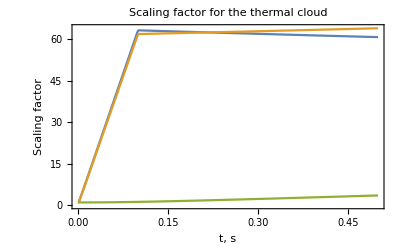
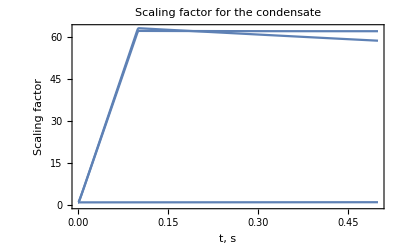
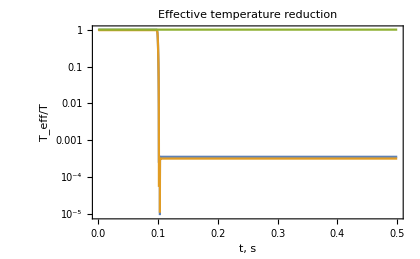

Final temperatures: {6.38908 pK,5.72129 pK,18309.5 pK}

Test on anharmonicities:

(-1.25237×10^-13 | 1. | -11234.3 | 1.23658×10^8 | -1.47594×10^12 | 1.92968×10^16 | -2.74569×10^20 | 4.20991×10^24 | -6.88827×10^28 | 1.193×10^33
2.07615×10^-6 | 0.0164566 | 260.885 | 6.20371×10^6 | 1.96695×10^11 | 7.79549×10^15 | 3.70745×10^20 | 2.05709×10^25 | 1.30444×10^30 | 9.30568×10^34)

{Failed,Failed,Failed,Failed,Failed,Failed,Passed,Passed}

```mathematica
(* Simulating the thermal component *)
nAtoms=Floor[Na(1-fc)];

(* WE REDUCED THE NUMBER OF ATOMS TO ACCELERATE THE COMPUTATION! The result does not change essentially *)
nAtoms=1000;

(* Time step and length of the simulation *)
tau =0.5;
dt = tau/500;
Ninc=Floor[20dt/dkkd]; (* increase in precision for the moment of dkc *)


force[t_,r_]:=-m ωt[t]^2 r(**UnitStep[r[[1]]+z1]*);
force[t_,r_]:=(ⅇ^(-(t-dkkt)^2/dkkd^2))*UnitBox[(t-dkkt)/(6dkkd)]*forceB[r[[1]],r[[2]],r[[3]]]*UnitStep[r[[1]]+z1];
(*force[t_,r_]:=UnitBox[(t-dkkt)/(2dkkd)]*forceB[r[[1]],r[[2]],r[[3]]];*)

propagate[t_,atom_,delt_]:={atom[[1]]+delt*atom[[2]]+(force[t,atom[[1]]]/m)delt^2/2,atom[[2]]+(force[t,atom[[1]]]/m)delt};

atoms=Transpose[{Transpose[RandomReal[NormalDistribution[0,#],nAtoms]&/@σ],RandomReal[NormalDistribution[0,Sqrt[kb*T/m]],{nAtoms,3}]}];
sigmas=Table[σ,{i,1,Floor[tau/dt+1]}];
Teff=Table[T*{1,1,1},{i,1,Floor[tau/dt+1]}];
timeline=Table[i*dt,{i,0,Floor[tau/dt]}];

For[Nt=1,Nt<=tau/dt,Nt++,
(* Increasing precision when applying dkc *)

If[ Abs[(Nt-1)dt-dkkt]<dkkd*3,
Do[atoms=propagate[(Nt-1)dt+i*dt/Ninc,#,dt/Ninc]&/@atoms,{i,0,Ninc-1}],
atoms=propagate[(Nt-1)dt,#,dt]&/@atoms
];

(*atoms=propagate[(Nt-1)dt,#,dt]&/@atoms;*)
Parray=First/@atoms;
meanParray=Mean[Parray];
sigmas[[Nt+1]]=Sqrt[Sum[(Parray[[i]]-meanParray)^2,{i,1,Length[Parray]}]/Length[Parray]];
Parray=Part[#,2]&/@atoms;
meanParray=Mean[Parray];
Teff[[Nt+1]]=(Sum[(Parray[[i]]-meanParray)^2,{i,1,Length[Parray]}]/Length[Parray])*(m/kb);
];

(* removing atoms that hit the chip *)
For[i=1,i≤Length[atoms],i++, If[atoms[[i,1,1]]≤-z1,atoms=Delete[atoms,i];i--]]

λth=Table[Interpolation[Transpose[{timeline,(Part[#,i]&/@sigmas)/σ[[i]]}]],{i,1,3}];

(* Simulating the condensate *)

λ[t_]={Subscript[λ, 1][t],Subscript[λ, 2][t],Subscript[λ, 3][t]};
sol=NDSolve[{Table[λ''[t][[j]]==ω[[j]]^2/(λ[t][[1]]λ[t][[2]]λ[t][[3]]λ[t][[j]])-(ωt[t][[j]])^2 λ[t][[j]],{j,1,3}],
λ[0]=={1,1,1},λ'[0]=={0,0,0}},λ[t],{t,0,tau}];


TeffoT=Table[Interpolation[Transpose[{timeline,(Part[#,i]&/@Teff)/T}]],{i,1,3}];
λthplot=Plot[{λth[[1]][t],λth[[2]][t],λth[[3]][t]},{t,0,tau},FrameLabel->{"t, s", "Scaling factor"},Frame->True, PlotLabel->"Scaling factor for the thermal cloud",
LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None],
Background->White,
ImageSize->400];

λcondplot=Plot[λ[t]/.sol,{t,0,tau},FrameLabel->{"t, s", "Scaling factor"},Frame->True, PlotLabel->"Scaling factor for the condensate",
LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None],
Background->White,
ImageSize->400];

Tplot=LogPlot[{TeffoT[[1]][t],TeffoT[[2]][t],TeffoT[[3]][t]},{t,0,tau},FrameLabel->{"t, s", "T_eff/T"},Frame->True, PlotLabel->"Effective temperature reduction",
LabelStyle->Directive[FontFamily->"Arial",FontColor->Black,FontSize->14,Background->None],
Background->White,
ImageSize->420];

{λthplot, λcondplot, Tplot}

Print["Final temperatures: ",Last[Teff]*10^12 "pK"]

nn=10;
Bn=Table[SeriesCoefficient[Series[ChipTrapField[x1,y1,z ,CLg1,CLd1,Bx1,By1],{z,z1,nn}],n]*Factorial[n],{n,1,nn}];
xf=sigmas[[Length[sigmas],1]];
xi=sigmas[[1,1]];
Print["Test on anharmonicities:"]
{Bn/Bn[[2]],Table[xi/xf((n-1)!)/xf^(n-2),{n,1,nn}]}//MatrixForm
Table[If[10*Abs[Bn[[n]]/Bn[[2]]]<xi/xf((n-1)!)/xf^(n-2),"Passed","Failed"],{n,3,nn}]
```

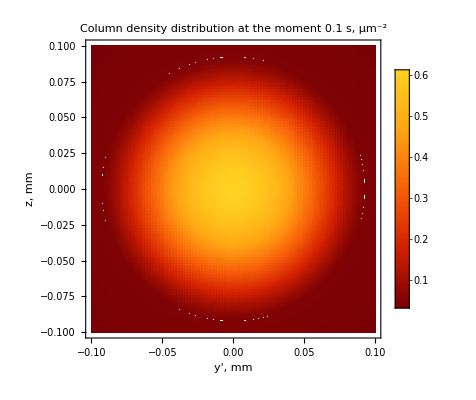

```mathematica
(* Density plot *)

R=1/ω √((hbar*ωbar)/m)(15 fc Na a √((m*ωbar)/hbar))^(1/5);
n2D[x_,y_]:=Na((1-fc)/(2π σ[[1]]σ[[2]])ⅇ^(-(x^2/(2 σ[[2]]^2)+y^2/(2 σ[[3]]^2)))+(5fc)/(2π R[[1]]R[[2]])Max[1-x^2/R[[1]]^2-y^2/R[[2]]^2,0]^(3/2))
n2Dt[x_,y_,t_]=(Na((1-fc)/(2π σ[[1]]σ[[2]]λth[[1]][t]λth[[2]][t])ⅇ^(-(x^2/(2 σ[[1]]^2(λth[[1]][t])^2)+y^2/(2 σ[[2]]^2(λth[[2]][t])^2)))+(5fc)/(2π R[[1]]R[[2]]Subscript[λ, 1][t]Subscript[λ, 2][t])Max[1-x^2/(R[[1]]^2(Subscript[λ, 1][t])^2)-y^2/(R[[2]]^2(Subscript[λ, 2][t])^2),0]^(3/2))/.sol)[[1]];
(*
LPlot=100*10^-6;
DensityPlot[n2Dt[x,y,dkkt]/10^12,{x,-LPlot,LPlot},{y,-LPlot,LPlot},PlotLegends->Automatic,PlotLabel->"Initial column density distribution at\n the moment of delta-kick cooling, μm^-2",PlotRange->All,PlotPoints->100,FrameLabel->{"x, m","
y, m"}]*)
tt=0.1;
LPlot=100*10^-6/mm;
DensityPlot[n2Dt[x mm,y mm,tt]/10^12,{x,-LPlot,LPlot},{y,-LPlot,LPlot},PlotLegends->Automatic,PlotLabel->"Column density distribution at\n the moment " <>ToString[tt]<>" s, μm^-2"(*,PlotRange->{Automatic,Automatic,{0, 1}}*),PlotPoints->100,FrameLabel->{"y', mm","
z, mm"},ColorFunction->"SolarColors"(*,ColorFunctionScaling->False*),ImageSize->400]
```

```mathematica
LPlot=0.0005;
{Animate[LogPlot[n2Dt[x,0,t]/10^12,{x,-LPlot,LPlot},PlotLegends->Automatic,PlotLabel->"Column density distribution, z=0, t="<>ToString[NumberForm[t,{3,3}]]<>" s",PerformanceGoal->"Quality", PlotRange->{{0,LPlot},{.0001,100}},Frame->True,Filling->Bottom,FrameLabel->{"Radial distance, m","Density, μm^-2"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Background->None],
Background->White,
ImageSize->420],{t,0,tau,dt}],Animate[Plot[n2Dt[x,0,t]/10^12,{x,-LPlot,LPlot},PlotLegends->Automatic,PlotLabel->"Column density distribution, z=0, t="<>ToString[NumberForm[t,{3,3}]]<>" s",PerformanceGoal->"Quality", PlotRange->{{0,LPlot},{0,1}},Frame->True,Filling->Bottom,FrameLabel->{"Radial distance, m","Density, μm^-2"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Background->None],
Background->White,
ImageSize->420],{t,0,tau,dt}]}
```

```mathematica
Graphics3D[{PointSize[Large],Point[First/@atoms]},Axes->True]
Graphics3D[{PointSize[Small],Point[Part[#,2]&/@atoms]},Axes->True]
```

-Graphics3D-

-Graphics3D-

```mathematica
forceB[x_,y_,z_]=-μB*{Interpolation[DBx][x,y,z],Interpolation[DBy][x,y,z],Interpolation[DBz][x,y,z]};
```

{-9.27×10^-24 (-3.6987×10^-11+71.8902 x-403818. x^2),-9.27×10^-24 (7.63233×10^-12+70.1384 y-0.00490122 y^2),-9.27×10^-24 (1.4162×10^-11+0.00700235 z+1.58652×10^-6 z^2)}

{-6.66422×10^-22,-6.50183×10^-22,-6.49118×10^-26}

{-6.72047×10^-22,-6.55677×10^-22,-5.97944×10^-26}

```mathematica
Ldist=0.00005;
Lz=0.002;
Npoints=10;
Npointsz=20;
aax=D[newfield[xx,y,z],xx]/.xx->x;
DBx=Flatten[ParallelTable[{{x,y,z},aax},{x,-Ldist,Ldist,Ldist/Npoints},{y,-Ldist,Ldist,Ldist/Npoints},{z,-Lz,Lz,Lz/Npointsz}],2];
aay=D[newfield[x,yy,z],yy]/.yy->y;
DBy=Flatten[ParallelTable[{{x,y,z},aay},{x,-Ldist,Ldist,Ldist/Npoints},{y,-Ldist,Ldist,Ldist/Npoints},{z,-Lz,Lz,Lz/Npointsz}],2];
aaz=D[newfield[x,y,zz],zz]/.zz->z;
DBz=Flatten[ParallelTable[{{x,y,z},aaz},{x,-Ldist,Ldist,Ldist/Npoints},{y,-Ldist,Ldist,Ldist/Npoints},{z,-Lz,Lz,Lz/Npointsz}],2];
forceB[x_,y_,z_]=-μB*{Interpolation[DBx][x,y,z],Interpolation[DBy][x,y,z],Interpolation[DBz][x,y,z]};
```

```mathematica
(* Here we calculate the mean and median size of the cloud, as well as the temperature of the central subcloud with radius "part" *)

part=.0001;
1000*Sqrt[Mean[(First/@atoms)^2]]"mm"
1000*Sqrt[Median[((Part[#,1]&/@atoms))^2]]"mm"
aver=Mean[((Part[#,2]&/@atoms))];
10^12(m/kb)*(Mean[((Part[#,2]&/@atoms))^2]-aver^2)"pK"
selected=Select[atoms,Sqrt[(#[[1,1]])^2+(#[[1,2]])^2]<part&];
Length[selected]"atoms"
aver=Mean[((Part[#,2]&/@selected))];
10^12(m/kb)*(Mean[((Part[#,2]&/@selected))^2]-aver^2)"pK"
{0.4139679048209038 "mm",0.017682678581404068 "mm",6.723505526918377 "mm"}
{0.1126580397352446 "mm",0.011999113990472323 "mm",4.580276979415273 "mm"}
{4893.943402562856 "pK",2.5639412984012324 "pK",18043.079562385337 "pK"}
463 "atoms"
{38.728514904386 "pK",2.5694666632545378 "pK",17042.71407667266 "pK"}
```

{0.614596 mm,0.142502 mm,0.738446 mm}

{0.167674 mm,0.0908307 mm,0.510155 mm}

{15677.4 pK,20.8022 pK,17506.2 pK}

191 atoms

{142.62 pK,18.0575 pK,17558.9 pK}

{0.413968 mm,0.0176827 mm,6.72351 mm}

{0.112658 mm,0.0119991 mm,4.58028 mm}

{4893.94 pK,2.56394 pK,18043.1 pK}

463 atoms

{38.7285 pK,2.56947 pK,17042.7 pK}

```mathematica
σ
R
freqs1
dkkt
dkkd
N[ωdkk/(2π)]
Last[sigmas]
R(λ[t]/.sol/.t->.1)[[1]]
Last[Teff]*10^12
D[newfield[0,y,0],{y,3}]/.y->0
D[newfield[x,0,0],{x,3}]/.x->0
z1
```

{2.07615×10^-6,2.09671×10^-6,0.000194622}

{1.47352×10^-6,1.48811×10^-6,0.00013813}

{100.18,99.1978,1.06868}

0.1

0.00125

{10.8159,10.7222,0.101764}

{0.00058364,0.000133493,0.000692331}

{0.0000926933,0.0000921638,0.00013961}

{21083.7,5.6071,18488.9}

-0.000119046

-807635.

0.00052659

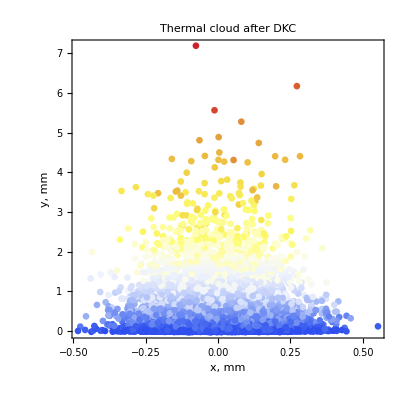

/Users/tigrank/Dropbox/CAL/temperaturelog.png

```mathematica
max=Max[Abs[Part[#,2]&/@atoms]];
Graphics[Table[{PointSize[0.012],ColorData["TemperatureMap"][(Log[10,1+9*atoms[[i,2,1]]/max])],Point[{atoms[[i,1,2]]*10^3,atoms[[i,1,1]]*10^3}]},{i,1,Length[atoms]}],Frame->True, AspectRatio->1,FrameLabel->{"x, mm","y, mm"},LabelStyle->Directive[FontFamily->"Arial",FontSize->14,FontColor->Black,Background->None],PlotLabel->"Thermal cloud after DKC"]
Export[NotebookDirectory[]<>"temperaturelog.png",%,ImageResolution->300]
```

```mathematica
(* Here we calculate the mean and median size of the cloud, as well as the temperature of the central subcloud with radius "part" *)

part=.00001;
1000*Sqrt[Mean[(First/@atoms)^2]]"mm"
1000*Sqrt[Median[((Part[#,1]&/@atoms))^2]]"mm"
aver=Mean[((Part[#,2]&/@atoms))];
10^12(m/kb)*(Mean[((Part[#,2]&/@atoms))^2]-aver^2)"pK"
selected=Select[atoms,Sqrt[(#[[1,1]])^2+(#[[1,2]])^2]<part&];
Length[selected]"atoms"
aver=Mean[((Part[#,2]&/@selected))];
10^12(m/kb)*(Mean[((Part[#,2]&/@selected))^2]-aver^2)"pK"
```

{0.673525 mm,0.134657 mm,0.746585 mm}

{0.168335 mm,0.0893221 mm,0.50348 mm}

{19177.9 pK,16.7345 pK,17909.2 pK}

47 atoms

{24.937 pK,9.75759 pK,19040.9 pK}

```mathematica
fc((kb*T)/(0.94*hbar*ωbar))^3/(1-fc) 
((kb*T)/(0.94*hbar*ωbar))^3
```

37497.6

37497.6

```mathematica
1.1/(87*1.66)Sqrt[3*105*5.3/(9.3*9.2*140)]
```

0.00284354

```mathematica
omega0=2π*100;
m0=87;
ma=1.66*10^(-27);
a0=(10^6)*Sqrt[hbar/(omega0*m0*ma)]"μm"
N0=1000;
N0/a0^2
```

1.07804 μm

860.461/μm^2